# Logcat

## Development Notebook

## Setup

```mathematica
Needs["Android`Logcat`"]
```

```mathematica
Needs["Utilities`Debug`"]
```

```mathematica
Needs["Calendar`"]
```

```mathematica
testDataDir=FileNameJoin[{ProjectDirectory["Android`Logcat`"],"TestData"}]
```

/Users/matt/WolframWorkspaces/Base2/Android/TestData

```mathematica
FileNames["*.txt",{testDataDir}]
```

{/Users/matt/WolframWorkspaces/Base2/Android/TestData/logcat.txt}

```mathematica
filePathName="logcat.txt";
```

```mathematica
filePath=FileNameJoin[{testDataDir,filePathName}]
```

/Users/matt/WolframWorkspaces/Base2/Android/TestData/logcat.txt

## Logcat

```mathematica
logcatData=LogcatData[filePath];
```

```mathematica
LogcatDataQ[logcatData]
```

True

```mathematica
FilePath[logcatData]
```

/Users/matt/WolframWorkspaces/Base2/Android/TestData/logcat.txt

```mathematica
Table[Timing[Length[Lines[logcatData]]],{3}]//TableForm
```

0.86377 | 3631
0.00753 | 3631
0.00006 | 3631

```mathematica
Map[LogcatLineQ,Lines[logcatData]]//Tally//Timing
```

{0.10175,{{True,3631}}}

```mathematica
Grid[Join[{{"LineNumber","Timestamp","PID","TID","LogLevel","LogTag","LogMessage"}},Transpose[Map[Thread,Through[{LineNumber,Timestamp,PID,TID,LogLevel,LogTag,LogMessage}[Lines[logcatData][[;;10]]]]]]/.dateList:_?DateQ:>DateString[dateList]],Alignment->{{Right,Left,Right,Right,Center,Left,Left},Automatic,{{1,1},{1,-1}}->Center},Dividers->{None,2->True},Frame->True,ItemSize->Full]
```

LineNumber | Timestamp | PID | TID | LogLevel | LogTag | LogMessage
2 | Tue 22 Apr 2014 08:53:06 | 157 | 157 | I | Vold | Vold 2.1 (the revenge) firing up
3 | Tue 22 Apr 2014 08:53:06 | 157 | 157 | E | Vold | Error reading configuration (No such file or directory)... continuing anyways
4 | Tue 22 Apr 2014 08:53:12 | 589 | 589 | I | SystemServer | Entered the Android system server!
5 | Tue 22 Apr 2014 08:53:12 | 589 | 607 | I | SystemServer | Waiting for installd to be ready.
6 | Tue 22 Apr 2014 08:53:12 | 589 | 607 | I | Installer | connecting...
7 | Tue 22 Apr 2014 08:53:12 | 589 | 607 | I | SystemServer | Entropy Mixer
8 | Tue 22 Apr 2014 08:53:12 | 589 | 607 | I | SystemServer | Power Manager
9 | Tue 22 Apr 2014 08:53:12 | 589 | 607 | I | SystemServer | Activity Manager
10 | Tue 22 Apr 2014 08:53:12 | 589 | 610 | I | ActivityManager | Memory class: 192
11 | Tue 22 Apr 2014 08:53:12 | 589 | 610 | I | UsageStats | Deleting usage file : usage-20130416

## GC

```mathematica
Reverse[SortBy[Tally[Map[LogLevel,Lines[logcatData]]],Last]]//TableForm
```

D | 2026
I | 998
E | 291
W | 284
V | 31
F | 1

```mathematica
Reverse[SortBy[Tally[Map[LogTag,Lines[logcatData]]],Last]]//TableForm
```

dalvikvm | 1378
ActivityManager | 523
jdwp | 230
ConnectivityService | 187
PackageManager | 122
ActivityThread | 98
YouTube | 74
com.appcelerator.cloud.push.PushService | 73
SystemServer | 63
alsa_ucm | 56
ALSAModule | 56
Gmail | 48
WindowManager | 46
AndroidRuntime | 33
ThrottleService | 32
dalvikvm-heap | 28
Module | 27
TiApplication | 24
System.out | 24
wpa_supplicant | 23
Tethering | 21
MtpService | 20
ApplicationContext | 17
ThermalDaemon | 16
ProcessStats | 16
overlay | 16
vpnandroid | 14
PhoneStatusBar | 13
BackupManagerService | 13
WindowState | 12
InputReader | 12
Adreno200-EGL | 12
InputMethodManagerService | 11
Icing | 11
DevicePolicyManagerService | 11
MountService | 10
GCMBroadcastReceiver | 10
PicasaUploaderSyncManager | 8
PicasaSyncManager | 8
PackageParser | 8
TiRootActivity | 7
AudioStreamOutALSA | 7
ACDB-LOADER | 7
UploadsManager | 6
SystemUpdateService | 6
SystemUIService | 6
RegisteredComponentCache | 6
Recovery | 6
qtaguid | 6
ProxyFactory | 6
PicasaUploader | 6
NetUtils | 6
libEGL | 6
JNIUtil | 6
GTalkService/c | 6
Finsky | 6
TiViewProxy | 5
SubscribedFeeds | 5
GCMBaseIntentService | 5
Settings | 4
PicasaUploaderSync | 4
PicasaSync | 4
DEBUG | 4
WiredAccessoryManager | 3
WifiStateMachine | 3
WifiService | 3
WalletApplication | 3
Smack/Packet | 3
ServiceDumpSys | 3
PowerManagerService | 3
NetworkManagementSocketTagger | 3
EventLogService | 3
CommandListener | 3
VoldCmdListener | 2
Vold | 2
Velvet.PerformanceTracker | 2
vclib | 2
TiLaunchActivity | 2
TiDbHelper | 2
TiAPI | 2
TiAnalyticsSvc | 2
TiAnalyticsDb | 2
SyncService | 2
StorageNotification | 2
SocketClient | 2
PowerUI | 2
PicasaPhotoCP | 2
MobileDataStateTracker | 2
LocationBlacklist | 2
InputManager | 2
IInputConnectionWrapper | 2
Genie | 2
CursorWrapperInner | 2
CountryDetector | 2
Zygote | 1
VoicemailCleanupService | 1
V8Object | 1
UsageStats | 1
TelephonyRegistry | 1
TapjoyModule | 1
SystemClock | 1
StatusBarManagerService | 1
StatusBar | 1
Search.LocationHelper | 1
PhoneStatusBar/NavigationBarView | 1
NsdService | 1
NetworkManagementService | 1
libc | 1
Installer | 1
DownloadManager | 1
DotsContentUris | 1
DotsApplication | 1
DockObserver | 1
DisplayManagerService | 1
DeadZone | 1
CrittercismAndroidModule | 1
Choreographer | 1
BroadcastQueue | 1
BootReceiver | 1

```mathematica
dalvikvmLines=Select[Lines[logcatData], StringMatchQ[LogTag[#], "dalvikvm"] &];
```

```mathematica
dalvikvmLogMessages=Map[LogMessage, dalvikvmLines];
```

```mathematica
Map[StringSplit[#][[1]]&,dalvikvmLogMessages]//Tally//SortBy[#,Last]&//Reverse//TableForm
```

GC_CONCURRENT | 613
GC_EXPLICIT | 437
DexOpt: | 68
GC_FOR_ALLOC | 66
WAIT_FOR_CONCURRENT_GC | 54
Trying | 37
Added | 37
No | 23
Total | 15
Debugger | 12
Turning | 4
Late-enabling | 3
Note: | 2
Jit: | 2
hprof: | 2
JIT | 1
GC | 1
dvmDdmHandleHpsgChunk(when | 1

### GC_CONCURRENT

```mathematica
gcConncurrentLines=Select[Lines[logcatData],StringMatchQ[LogMessage[#],StartOfString~~"GC_CONCURRENT"~~___]&];
```

```mathematica
gcConncurrentLogMessages=LogMessage/@gcConncurrentLines;
```

```mathematica
gcConncurrentLogMessages[[;;5]]
```

{GC_CONCURRENT freed 401K, 5% free 9846K/10276K, paused 2ms+3ms, total 26ms,GC_CONCURRENT freed 2529K, 34% free 19792K/29648K, paused 16ms+6ms, total 101ms,GC_CONCURRENT freed 968K, 12% free 12106K/13696K, paused 13ms+2ms, total 76ms,GC_CONCURRENT freed 364K, 5% free 10230K/10724K, paused 1ms+1ms, total 26ms,GC_CONCURRENT freed 974K, 12% free 12101K/13696K, paused 13ms+2ms, total 67ms}

```mathematica
gcConncurrentPattern=StartOfString ~~ "GC_CONCURRENT freed " ~~Repeated["<",{0,1}]~~ freed : DigitCharacter .. ~~ "K, " ~~ percentOfHeapFree : DigitCharacter .. ~~ "% free " ~~ usedHeapSize : DigitCharacter .. ~~ "K/" ~~ totalHeapSize : DigitCharacter .. ~~ "K, paused " ~~ pausedTime1 : DigitCharacter .. ~~ "ms+" ~~ pausedTime2 : DigitCharacter .. ~~ "ms, total " ~~ totalTime : DigitCharacter .. ~~ "ms" ~~ EndOfString;
```

```mathematica
StringMatchQ["GC_CONCURRENT freed 401K, 5% free 9846K/10276K, paused 2ms+3ms, total 26ms",gcConncurrentPattern]
```

True

```mathematica
StringMatchQ[#,gcConncurrentPattern]&/@gcConncurrentLogMessages//Tally
```

{{True,613}}

```mathematica
Select[gcConncurrentLogMessages,!StringMatchQ[#,gcConncurrentPattern]&]
```

{}

```mathematica
gcConcurrentData=Flatten/@StringCases[gcConncurrentLogMessages,gcConncurrentPattern:>Map[ToExpression,{freed,percentOfHeapFree,usedHeapSize,totalHeapSize,pausedTime1,pausedTime2,totalTime}]];
```

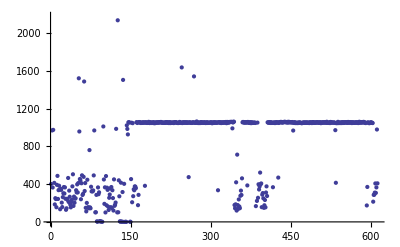
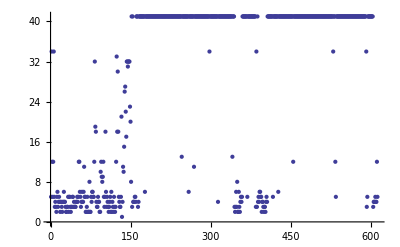
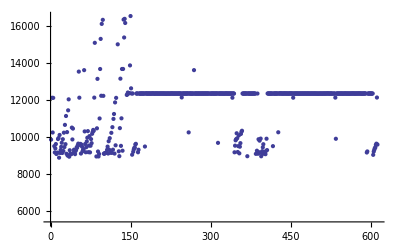
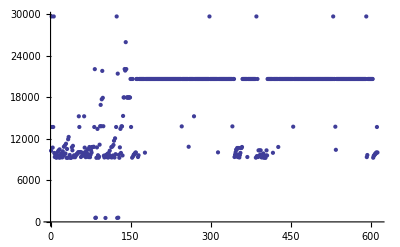
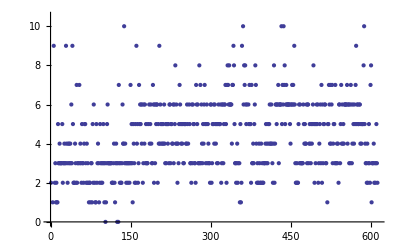
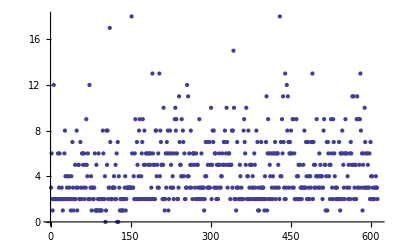
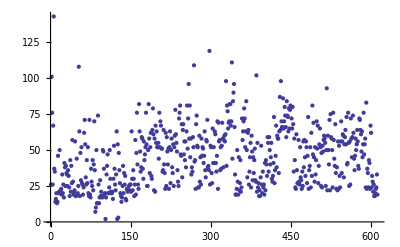

```mathematica
Map[ListPlot,Transpose[gcConcurrentData]]
```

### GC_EXPLICIT

```mathematica
gcExplicitLines=Select[Lines[logcatData],StringMatchQ[LogMessage[#],StartOfString~~"GC_EXPLICIT"~~___]&];
```

```mathematica
gcExplicitLogMessages=LogMessage/@gcExplicitLines;
```

```mathematica
gcExplicitLogMessages[[;;5]]
```

{GC_EXPLICIT freed 40K, 1% free 8825K/8892K, paused 2ms+7ms, total 45ms,GC_EXPLICIT freed <1K, 1% free 8825K/8892K, paused 4ms+2ms, total 26ms,GC_EXPLICIT freed <1K, 1% free 8825K/8892K, paused 1ms+2ms, total 17ms,GC_EXPLICIT freed 1898K, 34% free 19731K/29648K, paused 3ms+7ms, total 85ms,GC_EXPLICIT freed 1025K, 34% free 19705K/29648K, paused 10ms+8ms, total 120ms}

```mathematica
gcExplicitPattern=StartOfString ~~ "GC_EXPLICIT freed " ~~Repeated["<",{0,1}]~~ freed : DigitCharacter .. ~~ "K, " ~~ percentOfHeapFree : DigitCharacter .. ~~ "% free " ~~ usedHeapSize : DigitCharacter .. ~~ "K/" ~~ totalHeapSize : DigitCharacter .. ~~ "K, paused " ~~ pausedTime1 : DigitCharacter .. ~~ "ms+" ~~ pausedTime2 : DigitCharacter .. ~~ "ms, total " ~~ totalTime : DigitCharacter .. ~~ "ms" ~~ EndOfString;
```

```mathematica
StringMatchQ["GC_EXPLICIT freed 40K, 1% free 8825K/8892K, paused 2ms+7ms, total 45ms",gcExplicitPattern]
```

True

```mathematica
StringMatchQ[#,gcExplicitPattern]&/@gcExplicitLogMessages//Tally
```

{{True,437}}

```mathematica
Select[gcExplicitLogMessages,!StringMatchQ[#,gcExplicitPattern]&]
```

{}

```mathematica
gcExplicitData=Flatten/@StringCases[gcExplicitLogMessages,gcExplicitPattern:>Map[ToExpression,{freed,percentOfHeapFree,usedHeapSize,totalHeapSize,pausedTime1,pausedTime2,totalTime}]];
```

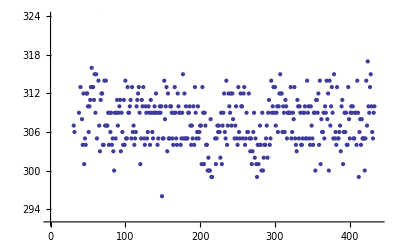
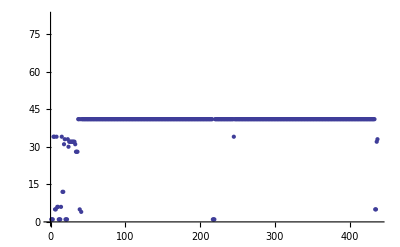
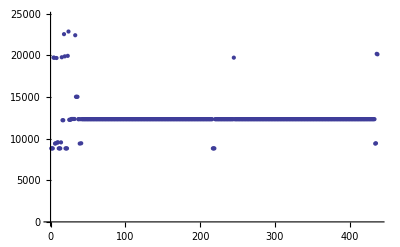
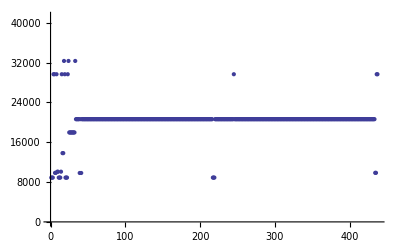
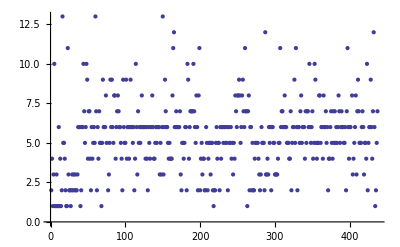
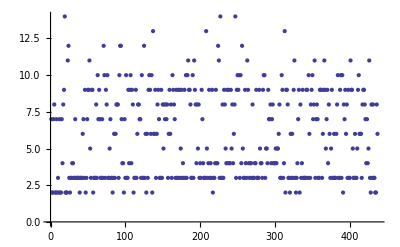
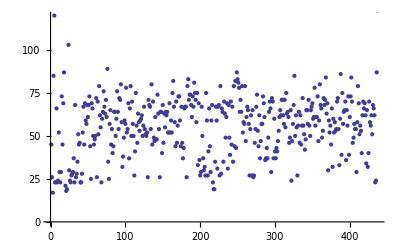

```mathematica
Map[ListPlot,Transpose[gcExplicitData]]
```

### GC_FOR_ALLOC

```mathematica
gcForAllocLines=Select[Lines[logcatData],StringMatchQ[LogMessage[#],StartOfString~~"GC_FOR_ALLOC"~~___]&];
```

```mathematica
gcForAllocLogMessages=LogMessage/@gcForAllocLines;
```

```mathematica
gcForAllocLogMessages[[;;5]]
```

{GC_FOR_ALLOC freed 1377K, 11% free 13579K/15240K, paused 76ms, total 77ms,GC_FOR_ALLOC freed 62K, 3% free 9931K/10188K, paused 38ms, total 38ms,GC_FOR_ALLOC freed 126K, 4% free 10059K/10444K, paused 41ms, total 41ms,GC_FOR_ALLOC freed 311K, 6% free 10013K/10588K, paused 26ms, total 26ms,GC_FOR_ALLOC freed 62K, 5% free 10077K/10588K, paused 15ms, total 15ms}

```mathematica
gcForAllocPattern=StartOfString ~~ "GC_FOR_ALLOC freed " ~~Repeated["<",{0,1}]~~ freed : DigitCharacter .. ~~ "K, " ~~ percentOfHeapFree : DigitCharacter .. ~~ "% free " ~~ usedHeapSize : DigitCharacter .. ~~ "K/" ~~ totalHeapSize : DigitCharacter .. ~~ "K, paused " ~~ pausedTime : DigitCharacter .. ~~ "ms, total " ~~ totalTime : DigitCharacter .. ~~ "ms" ~~ EndOfString;
```

```mathematica
StringMatchQ["GC_FOR_ALLOC freed 1377K, 11% free 13579K/15240K, paused 76ms, total 77ms",gcForAllocPattern]
```

True

```mathematica
StringMatchQ[#,gcForAllocPattern]&/@gcForAllocLogMessages//Tally
```

{{True,66}}

```mathematica
Select[gcForAllocLogMessages,!StringMatchQ[#,gcForAllocPattern]&]
```

{}

```mathematica
gcForAllocData=Flatten/@StringCases[gcForAllocLogMessages,gcForAllocPattern:>Map[ToExpression,{freed,percentOfHeapFree,usedHeapSize,totalHeapSize,pausedTime,totalTime}]];
```

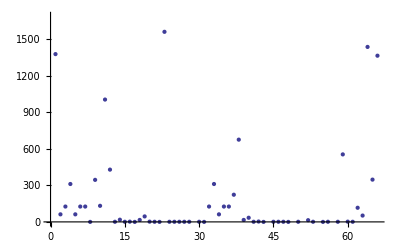
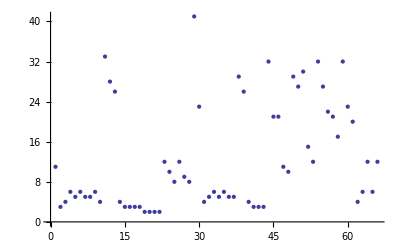
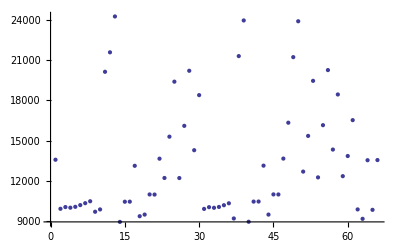
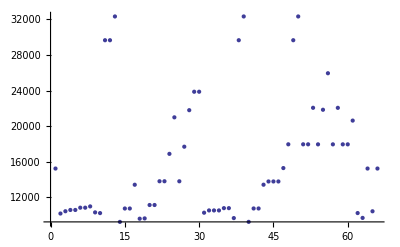
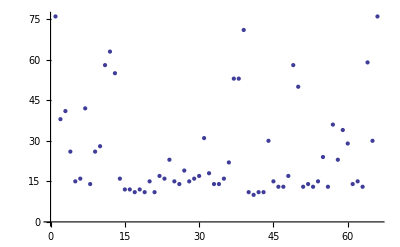
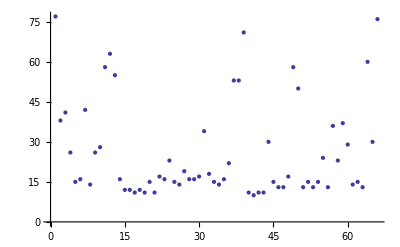

```mathematica
Map[ListPlot,Transpose[gcForAllocData]]
```

### WAIT_FOR_CONCURRENT

```mathematica
gcWaitForConcurrentLines=Select[Lines[logcatData],StringMatchQ[LogMessage[#],StartOfString~~"WAIT_FOR_CONCURRENT_GC"~~___]&];
```

```mathematica
gcWaitForConcurrentLogMessages=LogMessage/@gcWaitForConcurrentLines;
```

```mathematica
gcWaitForConcurrentLogMessages[[;;5]]
```

{WAIT_FOR_CONCURRENT_GC blocked 16ms,WAIT_FOR_CONCURRENT_GC blocked 9ms,WAIT_FOR_CONCURRENT_GC blocked 4ms,WAIT_FOR_CONCURRENT_GC blocked 5ms,WAIT_FOR_CONCURRENT_GC blocked 22ms}

```mathematica
gcWaitForConcurrentPattern=StartOfString ~~ "WAIT_FOR_CONCURRENT_GC blocked " ~~blockedTime : DigitCharacter .. ~~ "ms" ~~ EndOfString;
```

```mathematica
StringMatchQ["WAIT_FOR_CONCURRENT_GC blocked 16ms",gcWaitForConcurrentPattern]
```

True

```mathematica
StringMatchQ[#,gcWaitForConcurrentPattern]&/@gcWaitForConcurrentLogMessages//Tally
```

{{True,54}}

```mathematica
Select[gcWaitForConcurrentLogMessages,!StringMatchQ[#,gcWaitForConcurrentPattern]&]
```

{}

```mathematica
gcWaitForConcurrentData=Flatten[StringCases[gcWaitForConcurrentLogMessages,gcWaitForConcurrentPattern:>ToExpression[blockedTime]]];
```

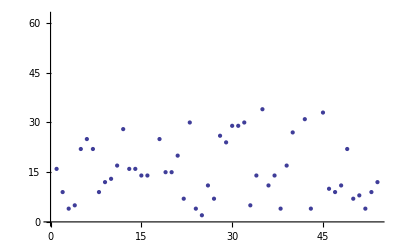

```mathematica
ListPlot[gcWaitForConcurrentData]
```